```mathematica
Select[Table[{n, GCD[3*n*(n+3),2*(n+1)*(n+2)]}, {n,1,50}],#[[2]]==6&][[All,1]]
```

{2,7,10,11,14,19,22,23,26,31,34,35,38,43,46,47,50}

```mathematica
ListLinePlot[%,Mesh->All]
```

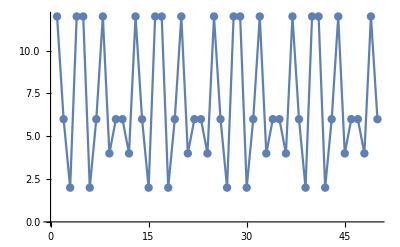
```mathematica
-Graphics-,{1,4,5,8}
```

```mathematica
F[n_, k_]:=1+(k-1)*Boole[CoprimeQ[n,k]]
```

```mathematica
Table[12*Boole[MemberQ[{1,4,5,8},Mod[n,12]]]-GCD[3*n*(n+3),2*(n+1)*(n+2)],{n,1,20}]
```

{0,-6,-2,0,0,-2,-6,0,-4,-6,-6,-4,0,-6,-2,0,0,-2,-6,0}